# CSE577 HW1 Shihuan Shao 1203060451

{{Null},{Null},{Null}}

{{Null},{Null}}

{{Null},{Null},{Null}}

{{Null},{Null}}

{{80,100},{20,100},{0,80},{0,60},{20,40},{20,20},{0,10},{20,0},{80,100},{100,90},{80,80},{80,60},{100,40},{100,20},{80,0},{20,0}}

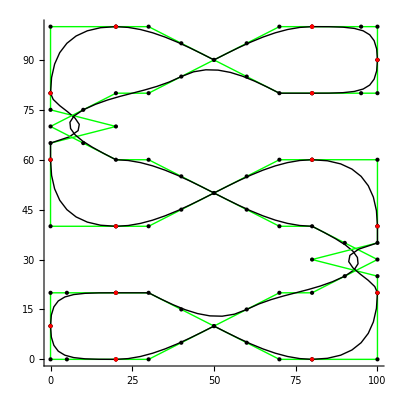

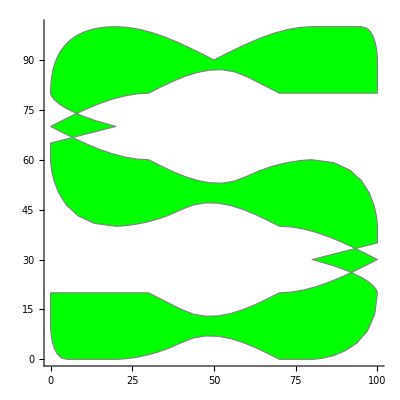

```mathematica
(*dca is used to calculate the points in the Bezier Curve, so that the curvy part can be integrated into a polygon to be colored. Those points are also used to create lines to color the curvy surfaces*)
dca[b_,r_,i_,t_]:=If [r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];

(*The left part of S *)
(*Point sets*)
s11={{80,100},{70,100},{60,95},{50,90},{40,95},{30,100},{20,100}};
s12={{20,100},{0,100},{0,80}};
s13={{0,80},{0,75},{20,70},{0,65},{0,60}};
s14={{0,60},{0,40},{20,40}};
s15={{20,40},{30,40},{40,45},{50,50},{60,45},{70,40},{80,40},{90,35},{100,30},{90,25},{80,20},{70,20},{60,15},{50,10},{40,15},{30,20},{20,20}};
s16={{20,20},{5,20},{0,20},{0,10}};
s17={{0,10},{0,0},{5,0},{20,0}};
(*Degree*)
d11=Length[s11]-1;
d12=2;
d13=Length[s13]-1;
d14=2;
d15=Length[s15]-1;
d16=3;
d17=3;
(*Curves*)
curve11=Graphics[{Thick,BezierCurve[s11,SplineDegree->d11]}];
curve12=Graphics[{Thick,BezierCurve[s12,SplineDegree->d12]}];
curve13=Graphics[{Thick,BezierCurve[s13,SplineDegree->d13]}];
curve14=Graphics[{Thick,BezierCurve[s14,SplineDegree->d14]}];
curve15=Graphics[{Thick,BezierCurve[s15,SplineDegree->d15]}];
curve16=Graphics[{Thick,BezierCurve[s16,SplineDegree->d16]}];
curve17=Graphics[{Thick,BezierCurve[s17,SplineDegree->d17]}];
(*Control polygon edges*)
poly11=Graphics[{Green,Line[s11]}];
poly12=Graphics[{Green,Line[s12]}];
poly13=Graphics[{Green,Line[s13]}];
poly14=Graphics[{Green,Line[s14]}];
poly15=Graphics[{Green,Line[s15]}];
poly16=Graphics[{Green,Line[s16]}];
poly17=Graphics[{Green,Line[s17]}];
(*Control points*)
points11=Graphics[{PointSize[Medium],Point[s11]}];
{{points12=Graphics[{PointSize[Medium],Point[s12]}];}, {points13=Graphics[{PointSize[Medium],Point[s13]}];}, {points14=Graphics[{PointSize[Medium],Point[s14]}];}}
{{points15=Graphics[{PointSize[Medium],Point[s15]}];}, {points16=Graphics[{PointSize[Medium],Point[s16]}];}}
points17=Graphics[{PointSize[Medium],Point[s17]}];
(*Lines calculated using dca*)
(*line11=Line[Table[dca[s11,d11,0,t],{t,0,1,0.05}]];*)
line12=Line[Table[dca[s12,d12,0,t],{t,0,1,0.01}]];
(*line13=Line[Table[dca[s13,d13,0,t],{t,0,1,0.05}]];
line14=Line[Table[dca[s14,d14,0,t],{t,0,1,0.05}]];
line15=Line[Table[dca[s15,d15,0,t],{t,0,1,0.05}]];
line16=Line[Table[dca[s16,d16,0,t],{t,0,1,0.05}]];
line17=Line[Table[dca[s17,d17,0,t],{t,0,1,0.05}]];*)
(*The right part of S *)
s21={{100,90},{100,100},{95,100},{80,100}};
s22={{80,80},{95,80},{100,80},{100,90}};
s23={{80,60},{70,60},{60,55},{50,50},{40,55},{30,60},{20,60},{10,65},{0,70},{10,75},{20,80},{30,80},{40,85},{50,90},{60,85},{70,80},{80,80}};
s24={{100,40},{100,60},{80,60}};
s25={{100,20},{100,25},{80,30},{100,35},{100,40}};
s26={{80,0},{100,0},{100,20}};
s27={{20,0},{30,0},{40,5},{50,10},{60,5},{70,0},{80,0}};
d21=3;
d22=3;
d23=Length[s23]-1;
d24=2;
d25=Length[s25]-1;
d26=2;
d27=Length[s27]-1;
curve21=Graphics[{Thick,BezierCurve[s21,SplineDegree->d21]}];
curve22=Graphics[{Thick,BezierCurve[s22,SplineDegree->d22]}];
curve23=Graphics[{Thick,BezierCurve[s23,SplineDegree->d23]}];
curve24=Graphics[{Thick,BezierCurve[s24,SplineDegree->d24]}];
curve25=Graphics[{Thick,BezierCurve[s25,SplineDegree->d25]}];
curve26=Graphics[{Thick,BezierCurve[s26,SplineDegree->d26]}];
curve27=Graphics[{Thick,BezierCurve[s27,SplineDegree->d27]}];
poly21=Graphics[{Green,Line[s21]}];
poly22=Graphics[{Green,Line[s22]}];
poly23=Graphics[{Green,Line[s23]}];
poly24=Graphics[{Green,Line[s24]}];
poly25=Graphics[{Green,Line[s25]}];
poly26=Graphics[{Green,Line[s26]}];
poly27=Graphics[{Green,Line[s27]}];
points21=Graphics[{PointSize[Medium],Point[s21]}];
{{points22=Graphics[{PointSize[Medium],Point[s22]}];}, {points23=Graphics[{PointSize[Medium],Point[s23]}];}, {points24=Graphics[{PointSize[Medium],Point[s24]}];}}
{{points25=Graphics[{PointSize[Medium],Point[s25]}];}, {points26=Graphics[{PointSize[Medium],Point[s26]}];}}
points27=Graphics[{PointSize[Medium],Point[s27]}];
(*line21=Line[Table[dca[s21,d21,0,t],{t,0,1,0.05}]];
line22=Line[Table[dca[s22,d22,0,t],{t,0,1,0.05}]];
line23=Line[Table[dca[s23,d23,0,t],{t,0,1,0.05}]];
line24=Line[Table[dca[s24,d24,0,t],{t,0,1,0.05}]];
line25=Line[Table[dca[s25,d25,0,t],{t,0,1,0.05}]];
line26=Line[Table[dca[s26,d26,0,t],{t,0,1,0.05}]];
line27=Line[Table[dca[s27,d27,0,t],{t,0,1,0.05}]];*)
(*Apply FilledCurve to fill the character with color*)
s=FilledCurve[{{BezierCurve[s11,SplineDegree->d11],line12,BezierCurve[s13,SplineDegree->5],BezierCurve[s14,SplineDegree->3],BezierCurve[s15,SplineDegree->17],BezierCurve[s16,SplineDegree->4],BezierCurve[s17,SplineDegree->4],
BezierCurve[s27,SplineDegree->7],BezierCurve[s26,SplineDegree->3],BezierCurve[s25,SplineDegree->5],BezierCurve[s24,SplineDegree->3],BezierCurve[s23,SplineDegree->17],BezierCurve[s22,SplineDegree->4],BezierCurve[s21,SplineDegree->4]}}];

graphs=Graphics[{EdgeForm[{Thick,Gray}],Green,s}];
(*End points are set red and large, other points are black and medium*)
end={{80,100},{20,100},{0,80},{0,60},{20,40},{20,20},{0,10},{20,0},{80,100},{100,90},{80,80},{80,60},{100,40},{100,20},{80,0},{20,0}}
endpts=Graphics[{PointSize[Large],Red,Point[end]}];
(*Show the plot with control polygon*)
Show[{
poly11,poly12,poly13,poly14,poly15,poly16,poly17,curve11,curve12,curve13,curve14,curve15,curve16,curve17,points11,points12,points13,points14,points15,points16,points17,
poly21,poly22,poly23,poly24,poly25,poly26,poly27,curve21,curve22,curve23,curve24,curve25,curve26,curve27,points21,points22,points23,points24,points25,points26,points27,
endpts
},Axes->True]
(*Show the plot with filled font. The routine of generating character C is almost similar with S. So no comments for C*)
Show[{graphs},Axes->True]
Manipulate[Graphics[{ColorData["Rainbow",x],s}],{x,0,1}]
```

{{Null},{Null},{Null}}

{{Null},{Null}}

{{Null},{Null}}

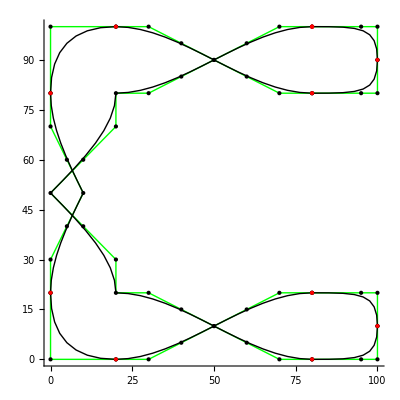

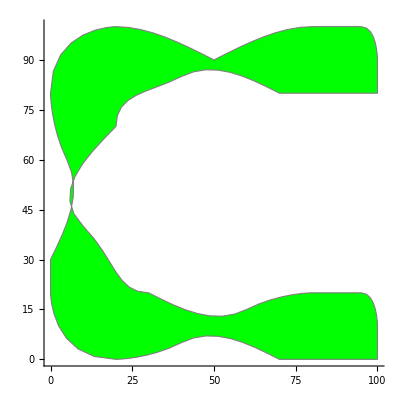

```mathematica
s11={{80,100},{70,100},{60,95},{50,90},{40,95},{30,100},{20,100}};
s12={{20,100},{0,100},{0,80}};
s13={{0,80},{0,70},{5,60},{10,50},{5,40},{0,30},{0,20}};
s14={{0,20},{0,0},{20,0}};
s15={{20,0},{30,0},{40,5},{50,10},{60,5},{70,0},{80,0}};
s16={{80,0},{95,0},{100,0},{100,10}};
s17={{100,10},{100,20},{95,20},{80,20}};
s18={{80,20},{70,20},{60,15},{50,10},{40,15},{30,20},{20,20},{20,30},{10,40},{0,50},{10,60},{20,70},{20,80},{30,80},{40,85},{50,90},{60,85},{70,80},{80,80}};
s19={{80,80},{95,80},{100,80},{100,90}};
s10={{100,90},{100,100},{95,100},{80,100}};
d11=Length[s11]-1;
d12=2;
d13=Length[s13]-1;
d14=2;
d15=Length[s15]-1;
d16=3;
d17=3;
d18=Length[s18]-1;
d19=3;
d10=3;
curve11=Graphics[{Thick,BezierCurve[s11,SplineDegree->d11]}];
curve12=Graphics[{Thick,BezierCurve[s12,SplineDegree->d12]}];
curve13=Graphics[{Thick,BezierCurve[s13,SplineDegree->d13]}];
curve14=Graphics[{Thick,BezierCurve[s14,SplineDegree->d14]}];
curve15=Graphics[{Thick,BezierCurve[s15,SplineDegree->d15]}];
curve16=Graphics[{Thick,BezierCurve[s16,SplineDegree->d16]}];
curve17=Graphics[{Thick,BezierCurve[s17,SplineDegree->d17]}];
curve18=Graphics[{Thick,BezierCurve[s18,SplineDegree->d18]}];
curve19=Graphics[{Thick,BezierCurve[s19,SplineDegree->d19]}];
curve10=Graphics[{Thick,BezierCurve[s10,SplineDegree->d10]}];
poly11=Graphics[{Green,Line[s11]}];
poly12=Graphics[{Green,Line[s12]}];
poly13=Graphics[{Green,Line[s13]}];
poly14=Graphics[{Green,Line[s14]}];
poly15=Graphics[{Green,Line[s15]}];
poly16=Graphics[{Green,Line[s16]}];
poly17=Graphics[{Green,Line[s17]}];
poly18=Graphics[{Green,Line[s18]}];
poly19=Graphics[{Green,Line[s19]}];
poly10=Graphics[{Green,Line[s10]}];
points11=Graphics[{PointSize[Medium],Point[s11]}];
{{points12=Graphics[{PointSize[Medium],Point[s12]}];}, {points13=Graphics[{PointSize[Medium],Point[s13]}];}, {points14=Graphics[{PointSize[Medium],Point[s14]}];}}
{{points15=Graphics[{PointSize[Medium],Point[s15]}];}, {points16=Graphics[{PointSize[Medium],Point[s16]}];}}
points17=Graphics[{PointSize[Medium],Point[s17]}];
{{points18=Graphics[{PointSize[Medium],Point[s18]}];}, {points19=Graphics[{PointSize[Medium],Point[s19]}];}}
points10=Graphics[{PointSize[Medium],Point[s10]}];
(*line11=Line[Table[dca[s11,d11,0,t],{t,0,1,0.05}]];*)
line12=Line[Table[dca[s12,d12,0,t],{t,0,1,0.05}]];
(*line13=Line[Table[dca[s13,d13,0,t],{t,0,1,0.05}]];
line14=Line[Table[dca[s14,d14,0,t],{t,0,1,0.05}]];
line15=Line[Table[dca[s15,d15,0,t],{t,0,1,0.05}]];
line16=Line[Table[dca[s16,d16,0,t],{t,0,1,0.05}]];
line17=Line[Table[dca[s17,d17,0,t],{t,0,1,0.05}]];
line18=Line[Table[dca[s18,d18,0,t],{t,0,1,0.05}]];
line19=Line[Table[dca[s19,d19,0,t],{t,0,1,0.05}]];
line10=Line[Table[dca[s10,d10,0,t],{t,0,1,0.05}]];*)
c=FilledCurve[{BezierCurve[s11,SplineDegree->d11],BezierCurve[s12,SplineDegree->3],BezierCurve[s13,SplineDegree->7],BezierCurve[s14,SplineDegree->3],BezierCurve[s15,SplineDegree->7],BezierCurve[s16,SplineDegree->4],BezierCurve[s17,SplineDegree->4],BezierCurve[s18,SplineDegree->19],BezierCurve[s19,SplineDegree->4],BezierCurve[s10,SplineDegree->4]}];
graphc=Graphics[{EdgeForm[{Thick,Gray}],Green,c}];
end={{80,100},{20,100},{0,80},{0,20},{20,0},{80,0},{100,10},{80,20},{80,80},{100,90},{80,100}};
endpts=Graphics[{PointSize[Large],Red,Point[end]}];

Show[{
poly11,poly12,poly13,poly14,poly15,poly16,poly17,poly18,poly19,poly10,curve11,curve12,curve13,curve14,curve15,curve16,curve17,curve18,curve19,curve10,points11,points12,points13,points14,points15,points16,points17,points18,points19,points10,
endpts
},Axes->True]

Show[{graphc},Axes->True]
Manipulate[Graphics[{ColorData["DarkRainbow",x],c}],{x,0,1}]
```

3D of these characters

Before this notebook, I wrote one which can generate 3D characters “S” and “C”. However, it took hours to evaluate each character, which is quite slow. So I took some time to run the code on my own computer, and copy-paste the generated letters here. They can be manipulated as if they are generated in this notebook. I hope I can get extra credits from them.

```mathematica
-Graphics3D--Graphics3D-

-Graphics3D--Graphics3D-
```